# Read Station Locations

```mathematica
(*Read 15 for station locations*)

r="C:\\Users\\Sam\\Desktop\\Thesis Work\\irene\\hurricane\\"
fpath15="C:\\Users\\Sam\\Desktop\\Thesis Work\\ADCIRC\\15s and stations\\irene\\spinup.15_withstations.txt";
stormname="hurricane";(*"spindown" or "spinup" or "hurricane"*)
boundary="Rock Springs";(*"Tarboro","Greenville","Pamlico", "Rock Springs", "Grimesland"*)
s15=OpenRead[fpath15];
raw=ReadList[s15,String];

Close[s15];
"Use this scroll bar to find the line # of first + last stations ('start' & 'end')"
Manipulate[raw[[i]],{i,1,Length[raw],1}]
```

C:\Users\Sam\Desktop\Thesis Work\irene\hurricane\

Use this scroll bar to find the line # of first + last stations ('start' & 'end')

# Set Initialization Values

```mathematica
(*start & end of the station list. Assumes the station locations are the same for 61 and 62*)
If[stormname=="spinup"∨stormname=="spindown",
start=906; (*start line of the stations*)
end=3583; (*end line of the stations*)
,
start=907;end=3584;
];

If[boundary=="Pamlico",
(*Pamlico at Washington - downstream boundary condition*)

xsecstart=192; (*of the stations, the number of the first of the boundary of interest.*)
xsecend=596; (*of the stations, the number of the end of the boundary of interest. *)
sitename="DS";
,
If[boundary=="Greenville",
(*Tar at Greenville - 02084000*)
xsecstart=51;
xsecend=99;
sitename="greenville"
,
If[boundary=="Tarboro",
(*Tar at tarboro? *)
xsecstart=9;
xsecend=37;
sitename="tarboro",
If[boundary=="Rock Springs",
xsecstart=1158;
xsecend=1178;
sitename="rock_springs",
If[boundary=="Grimesland",
xsecstart=2034;
xsecend=2054;
sitename="grimesland"
];
];
];
];
];


bathypath="C:\\Users\\Sam\\Desktop\\Thesis Work\\ADCIRC\\Data reading - bathymetries\\stationBathy.txt";(*text file. one column. one value for each station*)
path61=StringJoin[r,"fort.61"]; (*61 to use*)
wseoutpath=StringJoin[r,sitename,"_wse_full_",stormname,".txt"];(*output path for each boundary node's water surface elevations.*)
avgWSEoutpath=StringJoin[r,sitename,"_wse_median_",stormname,".txt"];(*output path for average downstream WSE*)
path62=StringJoin[r,"fort.62"];
davoutpath=StringJoin[r,sitename,"_dav_ts.txt"];
Qoutpath=StringJoin[r,sitename,"_Q_ts.txt"];
```

# Read 61 (Water Surface Elevation)

i

j

validation Table - should be list of station indexes, going from 1158 (xsecstart) to 1178 (xsecend)

Top

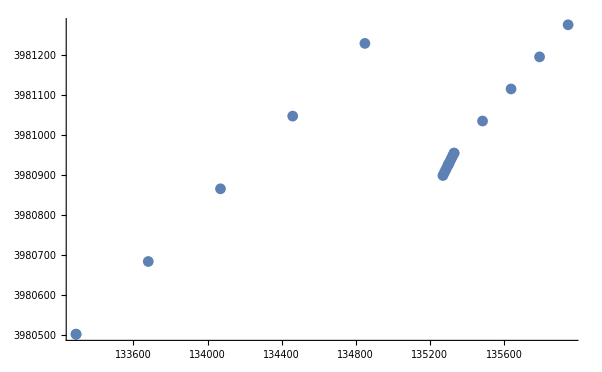

Front

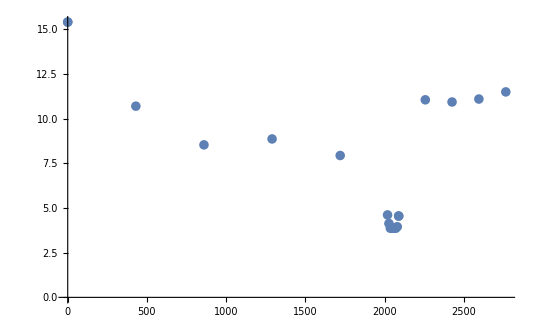

Shows the WSE timeseries at each node in xsection.

```mathematica
nstations=end-start+1;
(*
n61header=908;
n61headerstations=start-n61header;
n62header=;
n62stationstart=;
n62header=;
*)
"i"
Dynamic[i]
"j"
Dynamic[j]
StringJoin["validation Table - should be list of station indexes, going from ",ToString[xsecstart]," (xsecstart) to ",ToString[xsecend]," (xsecend)"]
Dynamic[validateTable]



stationlat=Table[0,{nstations}];
stationlon=Table[0,{nstations}];

s15=OpenRead[fpath15];
Skip[s15,String,(start-1)];

Do[
stationlon[[i]]=Read[s15,Number];
stationlat[[i]]=Read[s15,Number];
Skip[s15,String];
,{i,1,nstations}];

t=Read[s15,String];

Close[s15];


(* convert lat/longs into x/y *)
slam0=-79.0;(*center longitude*)
sfea0=35.0;(*center latitude*)
NAN="NAN";(*Designator for non-values*)

d2r=3.14159265358979323/180;
R=6378206.4;
slam0r=slam0*d2r;
sfea0r=sfea0*d2r;

slam=stationlon*d2r;
stationx=R*(slam-slam0r)*Cos[sfea0r];
sfea=stationlat*d2r;
stationy=R*sfea;
(*irene: last ds bc is at positions 192-596*)
lastx=stationx[[xsecstart;;xsecend]];
lasty=stationy[[xsecstart;;xsecend]];

"Top"
ListPlot[Transpose[Table[{lastx,lasty}]]]

(*import station bathymetries*)
bathystream=OpenRead[bathypath];
stationbathys=ReadList[bathystream];
lastz=stationbathys[[xsecstart;;xsecend]];
Close[bathystream];
dist=Table[((lastx[[i]]-Min[lastx])^2+(lasty[[i]]-Min[lasty])^2),{i,1,Length[lastx],1}];

"Front"
ListPlot[Transpose[Table[{Sqrt[dist],-1*lastz}]]]

(*Generate WSE timeseries at each station's points*)
s=OpenRead[path61];
temp=ReadList[s,String];
L=Length[temp];
Close[s];

(*import 61 timeseries for target x-section*)
totalstations=nstations;
timesteps=(L-2)/(totalstations+1);

xsecstations=xsecend-xsecstart+1;

ts=Table[Table[0,{timesteps}],{xsecstations}];	
validateTable=Table[0,{xsecstations}];

s=OpenRead[path61];
Skip[s,String,xsecstart+2];(* *)

Do[
Do[
validateTable[[i]]=Read[s,Number];
ts[[i,j]]=Read[s,Number];
,{i,1,xsecstations}];
Skip[s,String,totalstations+1-xsecstations];(*<-- Replace with the total number of stations - the number of stations before the target xsection *)
,{j,timesteps}];
Close[s];

Export[wseoutpath,ts];


"Shows the WSE timeseries at each node in xsection."
Manipulate[ListPlot[ts[[i]]],{i,1,Length[ts],1}]


(*this section calculates the average WSE at each timestep*)
WSEtimeseries=Transpose[ts];

Do[
	deletelist={};
	Do[
		If[WSEtimeseries[[i,j]]<-999,
			deletelist=Append[deletelist,{j}];
		]
	,{j,1,Length[WSEtimeseries[[i]]]}];
	WSEtimeseries[[i]]=Delete[WSEtimeseries[[i]],deletelist];
,{i,1,Length[WSEtimeseries]}];
```

middle station

3

median WSE timeseries at DS boundary

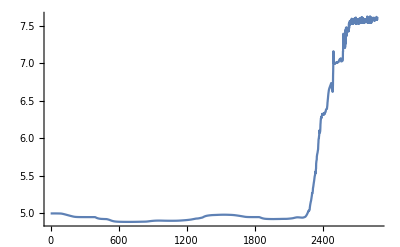

```mathematica
(*find the median station*)
medianvote=Table[0,{Length[WSEtimeseries]}];


Do[
	If[Mod[Length[WSEtimeseries[[i]]],2]==0, (*ensure an odd number of stations*)
		test=Flatten[Append[WSEtimeseries[[i]],0]];,
		test=WSEtimeseries[[i]];
	];
(*find location of median*)
medianvote[[i]]=Position[test,Median[test]][[1,1]]
,{i,1,Length[WSEtimeseries]}];
(*find median station timeseries*)
mid=Commonest[medianvote];
"middle station"
mid=mid[[1]]

If[boundary=="Grimesland",
mid=1;
];

WSEtimeseriesmedian=WSEtimeseries;
Do[
	If[WSEtimeseries[[i]]=={},
		WSEtimeseriesmedian[[i]]=NaN;,
		WSEtimeseriesmedian[[i]]=WSEtimeseries[[i,mid]];
	];
,{i,1,Length[WSEtimeseries]}];
Export[avgWSEoutpath,WSEtimeseriesmedian];

"median WSE timeseries at DS boundary"
ListPlot[WSEtimeseriesmedian,Joined->True]
```

# Read 62 (Depth-Averaged Velocity)

```mathematica
(* import 62 timeseries for last x-section*)
(*find file length*)
s=OpenRead[path62];
temp=ReadList[s,String];
L=Length[temp];
Close[s];


(*import file*)

totalstations=nstations;
timesteps=(L-2)/(totalstations+1);
"i"
Dynamic[i]
"j"
Dynamic[j]
StringJoin["validation Table - should be list of station indexes, going from ",ToString[xsecstart]," (xsecstart) to ",ToString[xsecend]," (xsecend)"]
Dynamic[validateTable]

s=OpenRead[path62];
Skip[s,String,2+xsecstart];(*<-- Replace with the total number of stations+3(for timestamp+headers) - number of stations before ds boundary (for each station at DS boundary). *)
davts=Table[Table[{0,0},{timesteps}],{xsecstations}];
validateTable=Table[0,{xsecstations}];

Do[
Do[
validateTable[[i]]=Read[s,Number];
davts[[i,j,1]]=Read[s,Number];
davts[[i,j,2]]=Read[s,Number];
,{i,1,xsecstations}];
Skip[s,String,totalstations+1-xsecstations];(*<-- Replace with the total number of stations +1(for timestamp) -13(for each station at DS boundary). *)
,{j,timesteps}];

Close[s];
Export[davoutpath,davts];
```

i

j

validation Table - should be list of station indexes, going from 51 (xsecstart) to 99 (xsecend)

# Calculate Depth Timeseries

```mathematica
(*use ts and stationbathys to calculate depth timeseries*)
dts=Table[Table[0,{j,1,timesteps}],{i,1,xsecstations}];
Do[
Do[
part1=ts[[i,j]];
part2=stationbathys[[xsecstart-1+i]];
If[part1=="NAN"∨part2=="NAN",
dts[[i,j]]=0;,
dts[[i,j]]=part1+part2;
];

,{j,1,timesteps}]
,{i,1,xsecstations}];


Do[
Do[
If[dts[[i,j]]<0,dts[[i,j]]=0]
,{i,1,xsecstations}];
,{j,1,timesteps}];


(*dts[[i,j]] represents the ith station, at timestep = j*)

(*calculate unit normal vectors for entire cross section*)
nsegs=xsecstations-1;

x=lastx;
y=lasty;

Quiet[
segns=Table[{x[[i]]-x[[i+1]],y[[i+1]]-y[[i]]}/((((x[[i]]-x[[i+1]])^2+(y[[i+1]]-y[[i]])^2))^(1/2)),{i,1,nsegs}];
segns=ReplacePart[segns,Position[segns,{Indeterminate,Indeterminate}]->{0,0}];
segLs=Table[(((x[[i]]-x[[i+1]])^2+(y[[i+1]]-y[[i]])^2))^(1/2),{i,1,nsegs}];
]
```

# Calculate Flow Timeseries

```mathematica
d2
```

d2

```mathematica
Qts=Table[0,{timesteps}];
Do[
Do[
u1v1=davts[[i,j]];
u2v2=davts[[i+1,j]];
d1=dts[[i,j]];
d2=dts[[i+1,j]];
n=segns[[i]];
Qseg=(Dot[n,u1v1]*d1/3)+(Dot[n,u1v1]*d2/6)+(Dot[n,u2v2]*d1/6)+(Dot[n,u2v2]*d2/3);
Qseg=Qseg*segLs[[i]];
Qts[[j]]=Qts[[j]]+Qseg;
,{i,1,xsecstations-1}];
,{j,1,timesteps}];
Export[Qoutpath,Qts];

"depth timeseries"
Manipulate[ListPlot[dts[[i]]],{i,1,Length[dts],1}]
```

depth timeseries

Part::partd: Part specification dts ⟦ 1 ⟧ is longer than depth of object.

ListPlot::lpn: dts ⟦ 1 ⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification dts ⟦ 1 ⟧ is longer than depth of object.

ListPlot::lpn: dts ⟦ 1 ⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification dts ⟦ 1 ⟧ is longer than depth of object.

ListPlot::lpn: dts ⟦ 1 ⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification dts ⟦ 1 ⟧ is longer than depth of object.

ListPlot::lpn: dts ⟦ 1 ⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification dts ⟦ 1 ⟧ is longer than depth of object.

ListPlot::lpn: dts ⟦ 1 ⟧ is not a list of numbers or pairs of numbers.

flow timeseries

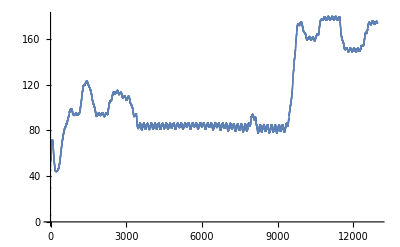

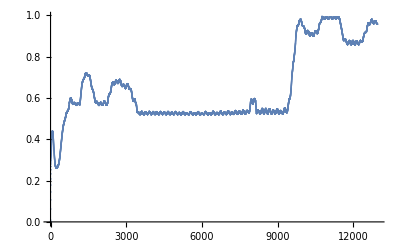

```mathematica
"flow timeseries"
ListPlot[Qts(*35.31466621266132*)]
ListPlot[WSEtimeseries]
```